# Thesis Workbook : How accurate is a clock?

## Main : Code To Be Used In Simulation :

This  section of the notebook contains the code for simulating the dynamics of the clock.
This is not the main simulation, that is contained within another section of this notebook.

```mathematica
Clear["Global`*"];
(* Set the number of levels for the system *)
(* This is the number of rungs on the ladder plus one for the holding level *)
NLevels =3; (* Rungs in ladder = NLevels -1 *)

(* Parameters *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =1(* γab : absorption rate *);
γh=10(* γh: absorption rate for holding level *);

(* Function for generating operators that cause transtions a <- b *)
sigmaminus[a_,b_] := Table[If[ i == a && j == b,1,0],{i,1,NLevels},{j,1,NLevels}];
(* This acts are our jump operator σ_ ,σ+ for  *)

(* We define the Hamiltonian *)
Hamiltonian := Table[If[ i == i && j == i,i*En,Ω],{i,1,NLevels},{j,1,NLevels}]
(* Generate Matrix for Our Hamiltonian *)
H=Hamiltonian  ;

(*Generating Symbolic density matric *)
ρ0= Table[ Subscript[ρ,i,j][t], {i,1,NLevels},{j,1,NLevels} ] (* Used Subscript[ρ,i,j] *);

(* Setting the values for the system : Will always start with p11 = 1 and the rest of the terms = 0 as will have a single load starting at the ground state *)
ρ01= Table[If[ i == 1 && j == 1,1,0],{i,1,NLevels},{j,1,NLevels}];

(*Terms for Emission and Absoprtion*)
emission =  γe (Sum[sigmaminus[i,i+1].ρ0 .Transpose[sigmaminus[i,i+1]]   - .5 (Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1].ρ0)  - .5 (ρ0.Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1]),{i,1,NLevels-2}]);
absorption= γab(Sum[Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]]),{i,1,NLevels-2}]) ; (*Same as emission, just swapping were the Transpose is *)

jumptohold=γh*(Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]])) /. i->(NLevels-1);


(* The Liouvillian *)
Ltotal = Chop[-ⅈ(H.ρ0-ρ0.H) + emission + absorption +jumptohold] ;
 (*This is what determines the dynamics of system and is what we will be solving*)

(* Solve System of ODEs *)
(*D[ρ0,t]  ==Ltotal; Derivate*)
(*(D[ρ0,t]/. t -> 0 ) == ρ01 ; Initial Conditions *)

(*Solved System of ODEs : s is an object containing the soltions for our ODEs for the populations and dehocences for our density matrix*)
s= NDSolve[{ (D[ρ0,t] ==Ltotal),(ρ0 /. t -> 0 ) == ρ01 },ρ0,{t,0,10}] ;
lables = Table[ρ0[[i ,i]],{i,1,Length[ρ0],1}] ;

emission
absorption
jumptohold
```

{{0.+ρ_(2,2)[t],0.-0.5 ρ_(1,2)[t],0.},{0.-0.5 ρ_(2,1)[t],-1. ρ_(2,2)[t],0.-0.5 ρ_(2,3)[t]},{0.,0.-0.5 ρ_(3,2)[t],0.}}

{{-1. ρ_(1,1)[t],0.-0.5 ρ_(1,2)[t],0.-0.5 ρ_(1,3)[t]},{0.-0.5 ρ_(2,1)[t],0.+ρ_(1,1)[t],0.},{0.-0.5 ρ_(3,1)[t],0.,0.}}

{{-10. ρ_(1,1)[t],-10. ρ_(1,2)[t],10 (0.-0.5 ρ_(1,3)[t])},{-10. ρ_(2,1)[t],10 (ρ_(1,1)[t]-1. ρ_(2,2)[t]),10 (0.+ρ_(1,2)[t]-0.5 ρ_(2,3)[t])},{10 (0.-0.5 ρ_(3,1)[t]),10 (0.+ρ_(2,1)[t]-0.5 ρ_(3,2)[t]),10 (0.+ρ_(2,2)[t])}}

## Plots :

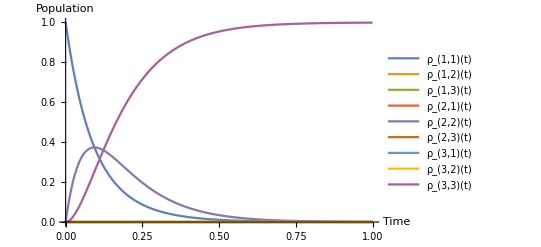

-Graphics-

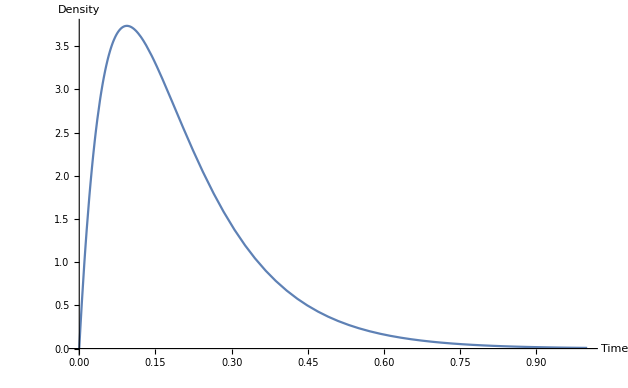

0.999007

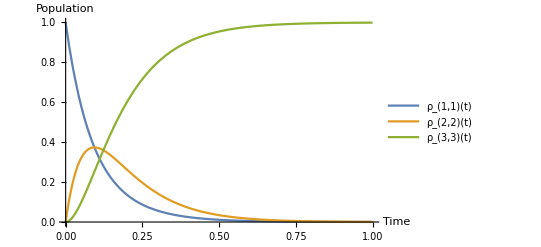

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.698817}}

```mathematica
(* Plotting holding level *)
(*Plot[{s[[1,4,2,4]],s[[1,2,2,2]]},{t,0,4},PlotRange->All,AxesLabel->{"Time","p"},AxesOrigin->{0,0},PlotLabels->{s[[1,4,1,4]],s[[1,2,1,2]]}]*)

s[[1,NLevels,1,NLevels]] ; (*Object I am intersted in , Row in denisty matrix , list that is the row (always 1), column*)
(* Getting All *) 
Table[s[[1,i,2,i]],{i,1,NLevels}] ;
(* Getting Populations*)
Populations = Table[ρ0[[i,i]],{i,1,NLevels}] (* Taking all the diagonal elements from the density matrix . Is a NLevles long list *);
Populationsresults = Table[s[[1,i,2,i]],{i,1,NLevels}]  (* Gets the InterpolatingFunction generated from solving the system of ODEs *);

(*Main Plot :  Populations and Degoherences *)
a = Flatten[s[[1,All,1,All]] ](* Lables *);
aa = Flatten[s[[1,All,2,All]] ](* InterpolatingFunctions *);
Plot[aa,{t,0,1},PlotRange->All,AxesLabel->{"Time","Population"},AxesOrigin->{0,0}, PlotLabel -> "",PlotLegends->a]

(* InterpolatingFunction generated for -> Holding Level *)
HoldingLevel = Populationsresults[[NLevels]] ;
HoldingLevelSolution = s[[1,NLevels,2,NLevels]] ;
Main2 = Plot[Populationsresults[[NLevels]],{t,0,1},PlotRange->All,AxesLabel->{"Time","Cumulative probability"},AxesOrigin->{0,0},PlotLabels-> Subscript[ρ,"N","N"]](* Plotting Population of Holding Level ONLY*)
(* Stats *)
tmax = 2 ;
pdf=D[HoldingLevelSolution,t]; (* Differentiate to get the probability density of the tick *)
mean=NIntegrate[pdf*t,{t,0,tmax}]; (* Mean tick interval *)
meansquare=NIntegrate[pdf*t^2,{t,0,tmax}]; (* Mean square tick interval *)
sdtick=Sqrt[meansquare-mean^2];

(* Plot pdf *) 
main = Plot[pdf,{t,0,1},PlotRange->All,AxesLabel->{"Time","Density"},AxesOrigin->{0,0}]
a =NIntegrate[pdf,{t,0,1}]


(* Plotting Populations (so no non diagonal components)*)
(* WANT TO ONLY PLOT THE POPULATIONS OF (SO NO NON DIGAGONAL ENTRIES)*)
Plot[Populationsresults,{t,0,1},PlotRange->All,AxesLabel->{"Time","Population"},AxesOrigin->{0,0},PlotLegends->lables]

(* Working out value of t to plot  ( FINDING APPORIATME VALUE OF t_max)*)
Solve[s[[1,NLevels,2,NLevels]]==0.99,t]
s[[1,NLevels,1,NLevels]] ;
```

## Stats :

These are the main stats that we will be concerned with 
→ Mean : 
→ Standard Deviation :

```mathematica
tmax=10
holdinpopfun=s[[1,NLevels,2,NLevels]]; (* This is the interpolating function generated above *)
pdf=D[holdinpopfun,t]; (* Differentiate to get the probability density of the tick *)
mean=NIntegrate[pdf*t,{t,0,tmax}]; (* Mean tick interval *)
meansquare=NIntegrate[pdf*t^2,{t,0,tmax}]; (* Mean square tick interval *)
sdtick=Sqrt[meansquare-mean^2];
```

10

## Main Simulation :

Function : For Key Calculations 
This  section of the notebook uses the code from pervious sections to run the simulation

```mathematica
meanandsd[NLevels_,γab_,γe_,γh_,tmax_]:=
(* This function packages all the above together, to solve the model for given parameters and return a list of the mean and standard deviation of the tick interval *)
(* Note new parameter tmax which is the maximum time up to which the dynaimcs is simulated *)
Module[{i,j,Ω,En,H,Ham,sigmaminus,emission,absorption,jumptohold,Ltotal,pop1,ρ01,s,holdinpopfun,HoldingLevel,pdf,mean,meansquare,sdtick,ρ0},

(* Parameters : For Hamiltonian *)
Ω=0; 
En = 1;
(* We define the Hamiltonian *)
(* Generate Matrix for Our Hamiltonian *)
H=Table[If[ i == i && j == i,i*En,Ω],{i,1,NLevels},{j,1,NLevels}] ;
Ham = -ⅈ(H.ρ0-ρ0.H);

ρ0= Table[ Subscript[ρ,i,j][t], {i,1,NLevels},{j,1,NLevels} ];
sigmaminus[a_,b_] := Table[If[ i == a && j == b,1,0],{i,1,NLevels},{j,1,NLevels}];
emission =  γe (Sum[sigmaminus[i,i+1].ρ0 .Transpose[sigmaminus[i,i+1]]   - .5 (Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1].ρ0)  - .5 (ρ0.Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1]),{i,1,NLevels-2}]);
absorption= γab(Sum[Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]]),{i,1,NLevels-2}]) ; 
jumptohold=γh*(Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]])) /. i->(NLevels-1);
(* and the Liouvillian- note I took out the Hamiltonian *)
Ltotal = Chop[   Ham+emission + absorption +jumptohold] ;
(* Initial state *)
(* Setting the values for the system : Will always start with p11 = 1 and the rest of the terms = 0 as will have a single load starting at the ground state *)
ρ01= Table[If[ i == 1 && j == 1,1,0],{i,1,NLevels},{j,1,NLevels}];
(* Solve System of ODEs *)
s = NDSolve[{ (D[ρ0,t] ==Ltotal),(ρ0 /. t -> 0 ) == ρ01 },ρ0,{t,0,tmax}] ;
holdinpopfun=s[[1,NLevels,2,NLevels]]; (* This is the interpolating function generated above *)

(* Getting Populations*)
HoldingLevel = ρ0[[NLevels,NLevels]] (*  *);

pdf=D[holdinpopfun,t]; (* Differentiate to get the probability density of the tick *)
mean=NIntegrate[pdf*t,{t,0,tmax}]; (* Mean tick interval *)
meansquare=NIntegrate[pdf*t^2,{t,0,tmax}]; (* Mean square tick interval *)
sdtick=Sqrt[meansquare-mean^2];
{mean,sdtick,HoldingLevel,holdinpopfun,pdf}
]

PlottingSimulation[varyn_,Values_,PlotName1_,tmaxPlot_,NumberOfInterpolatingFunctions_]:= 
(* This function generates the relavent plots for the results of the main simulation function *)
(*  NumberOfInterpolatingFunctions_ : The step size for the number of InterpolatingFunctions that are actually plotted*)
Module[{InterpolatingFunctions,lables},
(* 
	Plot1 : Mean tick interval 
  Plot2 : S.d. tick interval
  Plot3 : S.d. tick interval/Mean tick interval
Plot4 : Accuracy
Plot5 : Holding Levels (With Lable)
Plot6 : Holdng Levels (No Lables)
Plot7 : Resolution 



*)
InterpolatingFunctions = Table[varyn[[i,4]],{i,1,Length[varyn[[All,4]]],NumberOfInterpolatingFunctions}] ;(* InterpolatingFunctions *)
lables = Table[Values[[i]],{i,1,Length[varyn[[All,4]]],NumberOfInterpolatingFunctions}]; (* Lables for InterpolatingFunctions *)


{ListPlot[Transpose[{Values,varyn[[All,1]]}],AxesLabel->{PlotName1,"Mean tick interval"} ,AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 1 *),
ListPlot[Transpose[{Values,varyn[[All,2]]}],AxesLabel->{PlotName1,"S.d. tick interval"},AxesOrigin->{0,0} ,PlotRange->{{0,All},All}] (* Plot 2 *),
ListPlot[Transpose[{Values,varyn[[All,2]]/varyn[[All,1]]}],AxesLabel->{PlotName1,"S.d. tick interval/Mean tick interval"},AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 3 *),
ListPlot[Transpose[{Values,(varyn[[All,1]]/varyn[[All,2]])^2}],AxesLabel->{PlotName1,"Accuracy"},AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 4 *),
Plot[InterpolatingFunctions,{t,0,tmaxPlot},PlotRange->All,AxesLabel->{"Time",""},AxesOrigin->{0,0},PlotLabels->lables ,PlotLegends->lables] (* Plot 5 *), 
Plot[varyn[[All,4]],{t,0,tmaxPlot},PlotRange->All,AxesLabel->{"Time","p"},AxesOrigin->{0,0}] (* Plot 6 *),
ListPlot[Transpose[{Values,1/varyn[[All,1]]}],AxesLabel->{PlotName1,"Resolution"},AxesOrigin->{0,0},PlotRange->{{0,All},All}]


}
]
```

## Number of Level : NLevels

Investigating the relationship between the number of levels in the ladder and the tick statistics

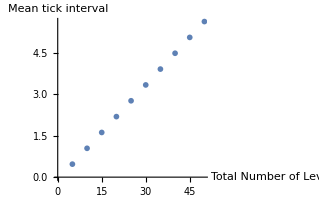
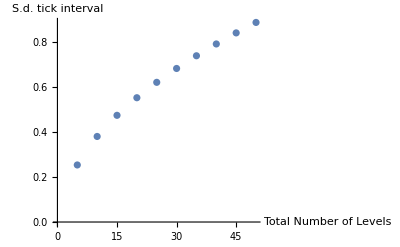
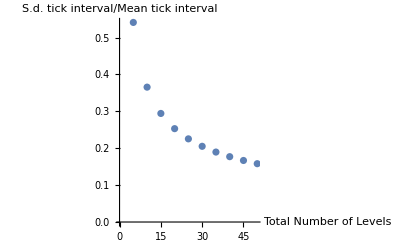
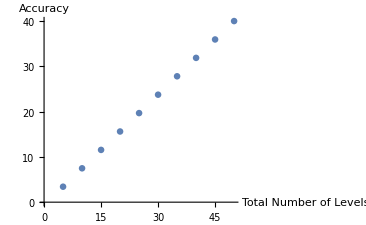
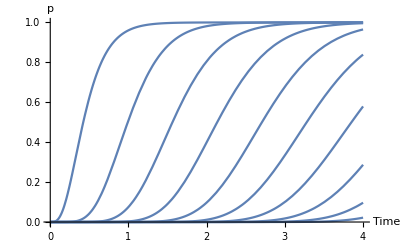
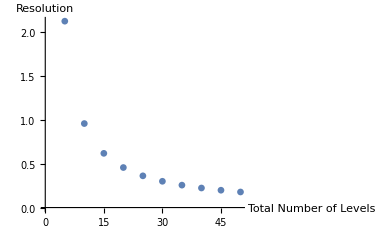
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Parameters : Simulation *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =Sqrt[3](* γab : absorption rate *);
γh=8 (* γh: absorption rate for holding level *);

(* Parameters : Plotting *)
tmaxPlot = 4;
NumberOfInterpolatingFunctions = 5;

nvalues=Table[nlevelsin,{nlevelsin,5,50,5}];
varyn=ParallelTable[meanandsd[nlevelsin,γab,γe,γh,20],{nlevelsin,nvalues}];
PlottingSimulation[varyn,nvalues,"Total Number of Levels",tmaxPlot,NumberOfInterpolatingFunctions]
```

## Rate :

This section investigates how the ration of these two quantieis might effect particular statistics of interest . One would expect that the greater the ratio the faster the ticks occur.

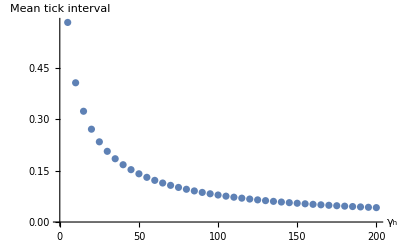
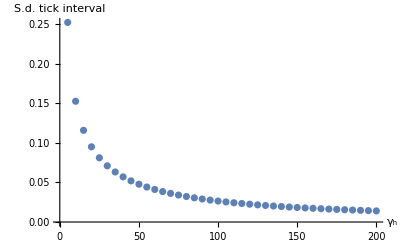
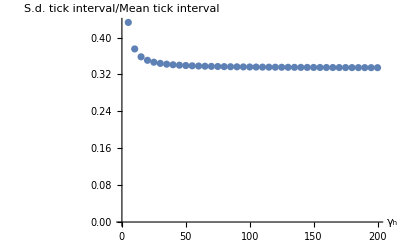
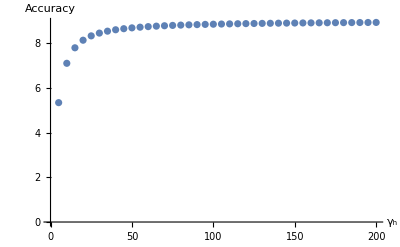
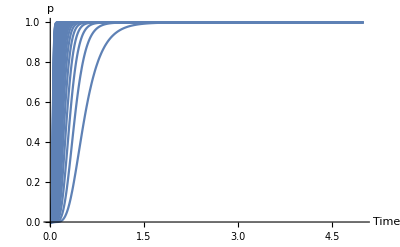
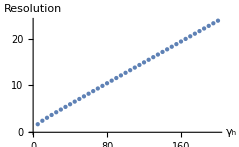
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Parameters : Simulation *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =Sqrt[300](* γab : absorption rate *);
γh=10 (* γh: absorption rate for holding level *);

(* Parameters : Plotting *)
tmaxPlot = 5;
NumberOfInterpolatingFunctions = 5 ; (* Plot every 5th that is calculated *)

RateValues=Table[i,{i,5,200,5}] ;
(* Rate Simulation*)
varyRate=ParallelTable[meanandsd[10,γab,γe,γh,tmaxPlot],{γh,RateValues}] ; (* Simulation : Parameter we are exmapining is the rate *)

(*Rate Plots*)
PlottingSimulation[varyRate,RateValues,,tmaxPlot,NumberOfInterpolatingFunctions]
```

## Ratio :

This section investigates how the rate at which absorption occurs to the holding level effects statistics of interest.

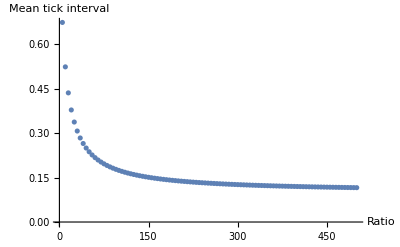
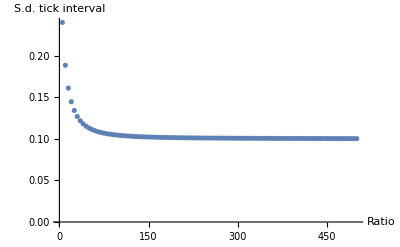
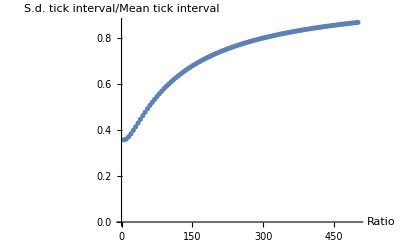
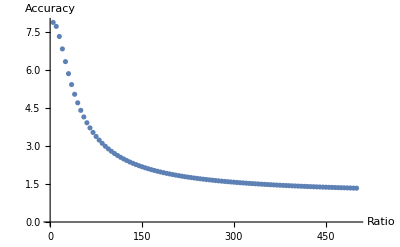
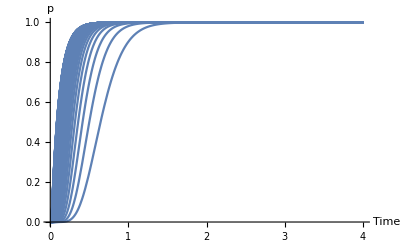
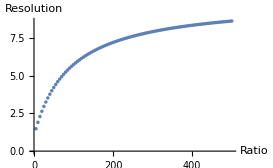
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Parameters *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =Sqrt[3](* γab : absorption rate *);
γh=10 (* γh: absorption rate for holding level *);

(* Parameters : Plotting *)
tmaxPlot = 4;
NumberOfInterpolatingFunctions = 5 ; (* Plot every 5th that is calculated *)

RatioValues=Table[i,{i,5,500,5}] ;
(*Ratio Simulation*)
varyRatio=ParallelTable[meanandsd[10,γab,γe,γh,tmaxPlot],{γab,RatioValues}] ; (* Simulation : Parameter we are exmapining is the ratio*)
(* Should run simulation where γab = γe *)

(*Ratio Plots*)
PlottingSimulation[varyRatio,RatioValues,"Ratio",tmaxPlot,NumberOfInterpolatingFunctions]
```

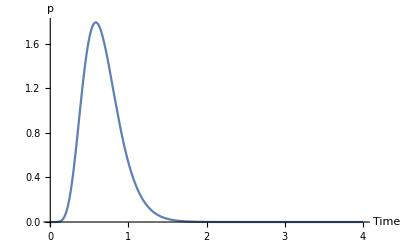

InterpolatingFunction::dmvali: The integration endpoint 10 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.+0. ⅈ

```mathematica
Plot[varyRatio[[1,5]],{t,0,4},PlotRange->All,AxesLabel->{"Time","p"},AxesOrigin->{0,0}]
mean=NIntegrate[varyRatio[[40,5]],{t,0,10}]
```

## Clock Accuracy For Varying Values of : NLevels ,

This section investigates how the rate at which absorption occurs to the holding level effects statistics of interest.

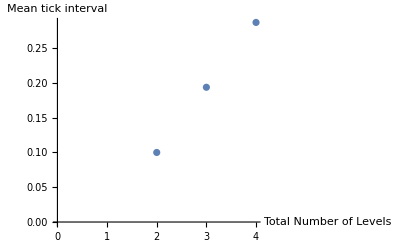
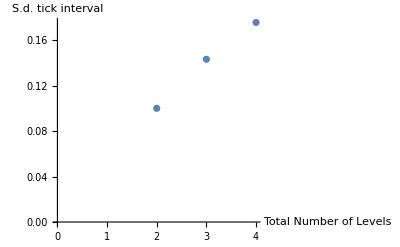
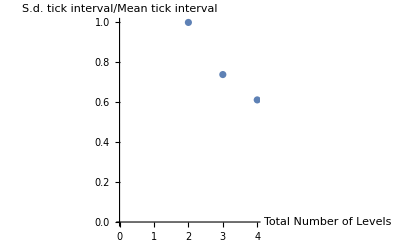
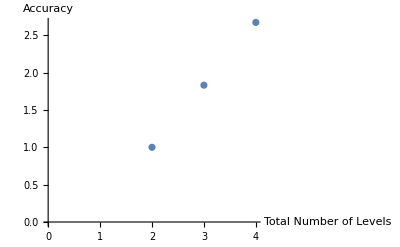
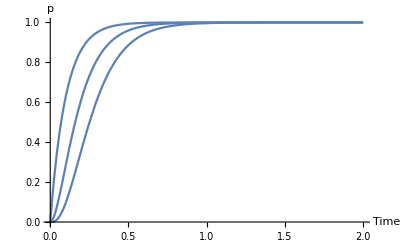
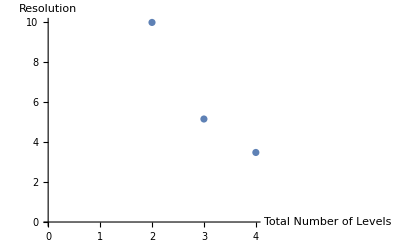
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Parameters *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =Sqrt[3](* γab : absorption rate *);
γh=10 (* γh: absorption rate for holding level *);

(* Parameters : Plotting *)
tmaxPlot = 2;
NumberOfInterpolatingFunctions = 5 ; (* Plot every 5th that is calculated *)

(* NLevels *) 
NLevelsValues = Table[nlevelsin,{nlevelsin,2,4,1}];
(* NLevels Simulation  *)
varyNLevels=ParallelTable[meanandsd[nlevelsin,γab,γe,γh,5],{nlevelsin,NLevelsValues}];
PlottingSimulation[varyNLevels,NLevelsValues,"Total Number of Levels",tmaxPlot,NumberOfInterpolatingFunctions]
```

```mathematica
RatioValues=Table[i,{i,5,200,5}] ;
(*Ratio Simulation*)
varyRatio=ParallelTable[meanandsd[10,γab,γe,γh,5],{γab,RatioValues}] ; (* Simulation : Parameter we are exmapining is the ratio*)
(* Should run simulation where γab = γe *)

(*Ratio Plots*)
(* PlottingSimulation[varyRatio,RatioValues,"",tmaxPlot,NumberOfInterpolatingFunctions]  *)
```

```mathematica
simulation[NLevels_,γab_,γe_,γh_,tmax_]:=
(* This function packages all the above together, to solve the model for given parameters and return a list of the mean and standard deviation of the tick interval *)
(* Note new parameter tmax which is the maximum time up to which the dynaimcs is simulated *)
Module[{i,j,Ω,En,H,Ham,sigmaminus,emission,absorption,jumptohold,Ltotal,pop1,ρ01,s,holdinpopfun,HoldingLevel,pdf,mean,meansquare,sdtick,ρ0,acc},

(* Parameters : For Hamiltonian *)
Ω=0; 
En = 1;

(* We define the Hamiltonian *)
(* Generate Matrix for Our Hamiltonian *)
H=Table[If[ i == i && j == i,i*En,Ω],{i,1,NLevels},{j,1,NLevels}] ;
Ham = -ⅈ(H.ρ0-ρ0.H);

ρ0= Table[ Subscript[ρ,i,j][t], {i,1,NLevels},{j,1,NLevels} ];
sigmaminus[a_,b_] := Table[If[ i == a && j == b,1,0],{i,1,NLevels},{j,1,NLevels}];
emission =  γe (Sum[sigmaminus[i,i+1].ρ0 .Transpose[sigmaminus[i,i+1]]   - .5 (Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1].ρ0)  - .5 (ρ0.Transpose[sigmaminus[i,i+1]].sigmaminus[i,i+1]),{i,1,NLevels-2}]);
absorption= γab(Sum[Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]]),{i,1,NLevels-2}]) ; 
jumptohold=γh*(Transpose[sigmaminus[i,i+1]].ρ0.sigmaminus[i,i+1]  - .5 (sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]].ρ0)  - .5 (ρ0.sigmaminus[i,i+1].Transpose[sigmaminus[i,i+1]])) /. i->(NLevels-1);
(* and the Liouvillian- note I took out the Hamiltonian *)
Ltotal = Chop[   Ham+emission + absorption +jumptohold] ;
(* Initial state *)
(* Setting the values for the system : Will always start with p11 = 1 and the rest of the terms = 0 as will have a single load starting at the ground state *)
ρ01= Table[If[ i == 1 && j == 1,1,0],{i,1,NLevels},{j,1,NLevels}];
(* Solve System of ODEs *)
s = NDSolve[{ (D[ρ0,t] ==Ltotal),(ρ0 /. t -> 0 ) == ρ01 },ρ0,{t,0,tmax}] ;
holdinpopfun=s[[1,NLevels,2,NLevels]]; (* This is the interpolating function generated above *)

(* Getting Populations*)
HoldingLevel = ρ0[[NLevels,NLevels]] (*  *);

pdf=D[holdinpopfun,t]; (* Differentiate to get the probability density of the tick *)
mean=NIntegrate[pdf*t,{t,0,tmax}]; (* Mean tick interval *)
meansquare=NIntegrate[pdf*t^2,{t,0,tmax}]; (* Mean square tick interval *)
sdtick=Sqrt[meansquare-mean^2];

{mean,sdtick,HoldingLevel,holdinpopfun,pdf,NLevels,γh}
]




(*meanandsd => simulation *)
```

```mathematica
(* Parameters *)
Ω=0; 
En = 1;
γe =  1(* γe : emission rate *); 
γab =Sqrt[3](* γab : absorption rate *);
γh=10 (* γh: absorption rate for holding level *);

NLevelsValues = Table[nlevelsin,{nlevelsin,5,20,5}] ;
RatioValues=Table[i,{i,25,30,5}] ;
 a = Table[ParallelTable[simulation[nlevelsin,γab,γe,ratevalues,15],{nlevelsin,NLevelsValues}] ,{ratevalues,RatioValues}] ; 
(* a = Table[Table[nlevelsin + γh ,{nlevelsin,NLevelsValues}] ,{γh,RatioValues}] *)
(* X = NLevelsValues *)
(* Y = RatioValues   *)
RatioValues
a[[1,All]] ; (* Column 1 : p_nlevelsin 1st value *)
a[[2,All]] ; (* Column 2 : p_nlevelsin 2nd value *)
MatrixForm[a]
```

{25,30}

((0.15663
0.0805547
ρ_(5,5)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
5
25) | (0.350941
0.120943
ρ_(10,10)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
10
25) | (0.545251
0.150882
ρ_(15,15)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
15
25) | (0.739561
0.175794
ρ_(20,20)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
20
25)
(0.130977
0.0670612
ρ_(5,5)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
5
30) | (0.293674
0.100677
ρ_(10,10)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
10
30) | (0.45637
0.125596
ρ_(15,15)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
15
30) | (0.619067
0.146332
ρ_(20,20)[t]
InterpolatingFunction[…][t]
InterpolatingFunction[…][t]
20
30))

The accuracy is shown as a function of d for different values of g (and fixed c=10 s−1),where[g]=EC.The
maximally achievable accuracy increases with decreasing g

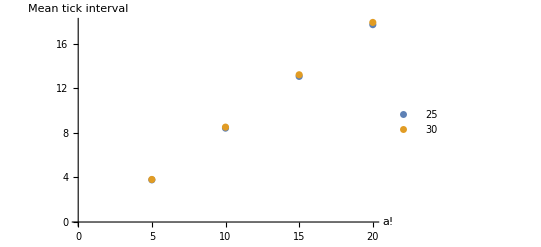

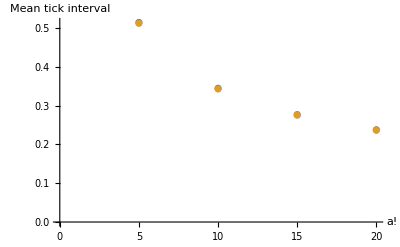

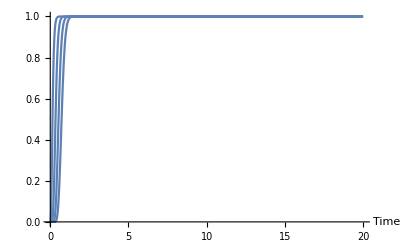

```mathematica
ListPlot[{Transpose[{NLevelsValues,(a[[1,All]][[All,1]]/a[[1,All]][[All,2]])^2}],Transpose[{NLevelsValues,(a[[2,All]][[All,1]]/a[[2,All]][[All,2]])^2}]},AxesLabel->{"a!","Mean tick interval"} ,AxesOrigin->{0,0},PlotRange->{{0,All},All},PlotLegends->RatioValues]
ListPlot[{Transpose[{NLevelsValues,(a[[1,All]][[All,2]]/a[[1,All]][[All,1]])}],Transpose[{NLevelsValues,(a[[2,All]][[All,2]]/a[[2,All]][[All,1]])}]},AxesLabel->{"a!","Mean tick interval"} ,AxesOrigin->{0,0},PlotRange->{{0,All},All}]
Plot[a[[1,All]][[All,4]],{t,0,20},PlotRange->All,AxesLabel->{"Time",""},AxesOrigin->{0,0}]
```

```mathematica
a[[1,All]][[,1]]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

{{0.15663,0.0805547,ρ_(5,5)[t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],5,25},{0.350941,0.120943,ρ_(10,10)[t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],10,25},{0.545251,0.150882,ρ_(15,15)[t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],15,25},{0.739561,0.175794,ρ_(20,20)[t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],20,25}}⟦Null,1⟧

Part::partd: Part specification Values⟦1⟧ is longer than depth of object.

Part::partd: Part specification Values⟦6⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Values,{0.469761,1.04237,1.61497,2.18757,2.76017,3.33278,3.90538,4.47798,5.05059,5.62319}} cannot be transposed.

ListPlot::lpn: Transpose[{Values,{0.469761,1.04237,1.61497,2.18757,2.76017,3.33278,3.90538,4.47798,5.05059,5.62319}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Values,{0.469761,1.04237,1.61497,2.18757,2.76017,3.33278,3.90538,4.47798,5.05059,5.62319}}],AxesLabel→{PlotName1,Mean tick interval},AxesOrigin→{0,0},PlotRange→{{0,All},All}]

Transpose::nmtx: The first two levels of {Values,{0.254066,0.38098,0.47512,0.553475,0.622035,0.683755,0.74035,0.792911,0.842203,0.888766}} cannot be transposed.

ListPlot::lpn: Transpose[{Values,{0.254066,0.38098,0.47512,0.553475,0.622035,0.683755,0.74035,0.792911,0.842203,0.888766}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Values,{0.254066,0.38098,0.47512,0.553475,0.622035,0.683755,0.74035,0.792911,0.842203,0.888766}}],AxesLabel→{PlotName1,S.d. tick interval},AxesOrigin→{0,0},PlotRange→{{0,All},All}]

Transpose::nmtx: The first two levels of {Values,{0.54084,0.365496,0.294198,0.253009,0.225361,0.205161,0.189572,0.177069,0.166753,0.158054}} cannot be transposed.

ListPlot::lpn: Transpose[{Values,{0.54084,0.365496,0.294198,0.253009,0.225361,0.205161,0.189572,0.177069,0.166753,0.158054}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Values,{0.54084,0.365496,0.294198,0.253009,0.225361,0.205161,0.189572,0.177069,0.166753,0.158054}}],AxesLabel→{PlotName1,S.d. tick interval/Mean tick interval},AxesOrigin→{0,0},PlotRange→{{0,All},All}]

Transpose::nmtx: The first two levels of {Values,{3.41871,7.48574,11.5537,15.6217,19.6899,23.7581,27.8261,31.8945,35.9625,40.0305}} cannot be transposed.

ListPlot::lpn: Transpose[{Values,{3.41871,7.48574,11.5537,15.6217,19.6899,23.7581,27.8261,31.8945,35.9625,40.0305}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Values,{3.41871,7.48574,11.5537,15.6217,19.6899,23.7581,27.8261,31.8945,35.9625,40.0305}}],AxesLabel→{PlotName1,Accuracy},AxesOrigin→{0,0},PlotRange→{{0,All},All}]

-Graphics-

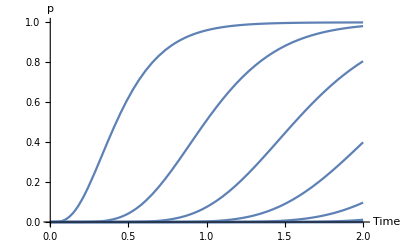

```mathematica
(* Plotting *)
InterpolatingFunctions = Table[varyn[[i,4]],{i,1,Length[varyn[[All,4]]],NumberOfInterpolatingFunctions}] ;(* InterpolatingFunctions *)
lables = Table[Values[[i]],{i,1,Length[varyn[[All,4]]],NumberOfInterpolatingFunctions}]; (* Lables for InterpolatingFunctions *)


ListPlot[Transpose[{Values,varyn[[All,1]]}],AxesLabel->{PlotName1,"Mean tick interval"} ,AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 1 *)
ListPlot[Transpose[{Values,varyn[[All,2]]}],AxesLabel->{PlotName1,"S.d. tick interval"},AxesOrigin->{0,0} ,PlotRange->{{0,All},All}] (* Plot 2 *)
ListPlot[Transpose[{Values,varyn[[All,2]]/varyn[[All,1]]}],AxesLabel->{PlotName1,"S.d. tick interval/Mean tick interval"},AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 3 *)
ListPlot[Transpose[{Values,(varyn[[All,1]]/varyn[[All,2]])^2}],AxesLabel->{PlotName1,"Accuracy"},AxesOrigin->{0,0},PlotRange->{{0,All},All}] (* Plot 4 *)
Plot[InterpolatingFunctions,{t,0,tmaxPlot},PlotRange->All,AxesLabel->{"Time",""},AxesOrigin->{0,0},PlotLabels->lables ,PlotLegends->lables] (* Plot 5 *)
Plot[varyn[[All,4]],{t,0,tmaxPlot},PlotRange->All,AxesLabel->{"Time","p"},AxesOrigin->{0,0}](* Plot 6 *)
```

```mathematica
(a[[1,All]][[All,1]])^2/(a[[1,All]][[All,2]])^2
```

{3.78068,8.41985,13.0592,17.6985}

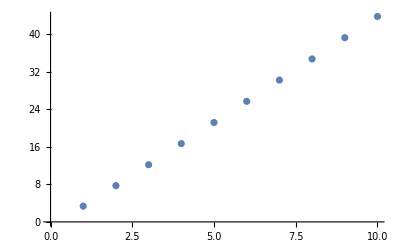

```mathematica
ListPlot[{3.3520954472584825,7.713443372245623,12.172646288412453,16.661725362216444,21.163851528711994,25.672844546544052,30.185935936466485,34.7017044851012,39.219127034659216,43.73775351779414}]
```

```mathematica
(a[[1,All]][[All,1]])
```

{0.15663,0.350941,0.545251,0.739561}

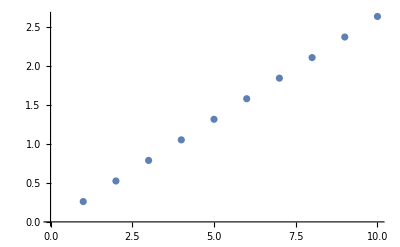

-Graphics-

```mathematica
ListPlot[{0.26038748266229744,0.5235457165823869,0.7867036094896592,1.0498615981379116,1.3130194827954786,1.57617731255679,1.839335205324452,2.1024928016425566,2.365650818565256,2.6288086307371863}]
```